# Generalized Roche/Kopal potential

Author : Martin Horvat, April 2016

## Defining potential

```mathematica
(* Generalized Roche/Kopal potential *)
```

```mathematica
Omega[x_,y_,z_,{q_,F_,d_}]=FullSimplify[1/Sqrt[x^2+y^2+z^2]+q(1/Sqrt[x^2+y^2+z^2-2x d+d^2]-x/d^2)+1/2F^2(1+q)(x^2+y^2)]
```

-(q x)/d^2+1/2 F^2 (1+q) (x^2+y^2)+q/(√((d-x)^2+y^2+z^2))+1/(√(x^2+y^2+z^2))

```mathematica
(* Gradient of the potential *)
```

```mathematica
DOmega[x_,y_,z_,{q_,F_,d_}]=FullSimplify[-D[Omega[x,y,z,{q,F,d}],{{x,y,z}}]]
```

{q/d^2-F^2 (1+q) x+(q (-d+x))/(((d-x)^2+y^2+z^2)^(3/2))+x/((x^2+y^2+z^2)^(3/2)),-F^2 (1+q) y+y (q/(((d-x)^2+y^2+z^2)^(3/2))+1/((x^2+y^2+z^2)^(3/2))),(q z)/(((d-x)^2+y^2+z^2)^(3/2))+z/((x^2+y^2+z^2)^(3/2))}

```mathematica
DDOmega[x_,y_,z_,{q_,F_,d_}]=FullSimplify[D[DOmega[x,y,z,{q,F,d}],{{x,y,z}}]]
```

{{-F^2 (1+q)+(q (-2 (d-x)^2+y^2+z^2))/(((d-x)^2+y^2+z^2)^(5/2))+(-2 x^2+y^2+z^2)/((x^2+y^2+z^2)^(5/2)),(3 q (d-x) y)/(((d-x)^2+y^2+z^2)^(5/2))-(3 x y)/((x^2+y^2+z^2)^(5/2)),(3 q (d-x) z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 x z)/((x^2+y^2+z^2)^(5/2))},{y ((3 q (d-x))/(((d-x)^2+y^2+z^2)^(5/2))-(3 x)/((x^2+y^2+z^2)^(5/2))),-F^2 (1+q)+(q ((d-x)^2-2 y^2+z^2))/(((d-x)^2+y^2+z^2)^(5/2))+(x^2-2 y^2+z^2)/((x^2+y^2+z^2)^(5/2)),y (-(3 q z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 z)/((x^2+y^2+z^2)^(5/2)))},{(3 q (d-x) z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 x z)/((x^2+y^2+z^2)^(5/2)),-(3 q y z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 y z)/((x^2+y^2+z^2)^(5/2)),q/(((d-x)^2+y^2+z^2)^(3/2))+1/((x^2+y^2+z^2)^(3/2))+z^2 (-(3 q)/(((d-x)^2+y^2+z^2)^(5/2))-3/((x^2+y^2+z^2)^(5/2)))}}

```mathematica
(* Gradient of the potential along x-axis *)
```

```mathematica
DOmega[x,0,0,{q,F,d}]
```

{q/d^2-F^2 (1+q) x+x/((x^2)^(3/2))+(q (-d+x))/(((d-x)^2)^(3/2)),0,0}

```mathematica
(* Rescaled potential along x-axis and rescaled parameter *)
```

```mathematica
OmegaX[t_,{q_,F_}]=FullSimplify[d Omega[d t,0,0,{q,F,d}],d>0&&t∈Reals]/.F^2d^3->a
```

1/2 (-2 q t+a (1+q) t^2+(2 q)/Abs[-1+t]+2/Abs[t])

## Points on x - axis at reference potential Omega0

Searching for x such that
	Omega(x,0,0) = Omega0

Introducing constant:
	a=d^3 F^2
	b=a(1+q) or b = a(1+p)
	rO = delta Omega0;

```mathematica
(* x< 0: x= -delta t => t>0*)
L1=Collect[
Numerator[
Together[
FullSimplify[OmegaX[-t,{q,F}]-rO,t>0]/.a->b1/(1+q)
]
],t,Simplify]
```

2+2 (1+q-rO) t+2 (q-rO) t^2+(b1+2 q) t^3+b1 t^4

```mathematica
CForm/@CoefficientList[L1,t]
```

{2,2*(1 + q - rO),2*(q - rO),b1 + 2*q,b1}

```mathematica
(* x in [0,delta], x = delta t => t in [0,1]*)
C1=Collect[
Numerator[
Together[
FullSimplify[OmegaX[t,{q,F}]-rO,0<t< 1]/.a->b1/(1+q)
]
],t,Simplify]
```

-2+(2-2 q+2 rO) t+2 (q-rO) t^2+(-b1-2 q) t^3+b1 t^4

```mathematica
CForm/@FullSimplify[CoefficientList[C1,t]]
```

{-2,2 - 2*q + 2*rO,2*(q - rO),-b1 - 2*q,b1}

```mathematica
(* x> delta, x = delta(1+ t) => t > 0*)
R1=Collect[
Numerator[
Together[
FullSimplify[OmegaX[t+1,{1/p,F}]-rO,t>0]/.a->b2/(1+p)
]
],t,Simplify]
```

2+(b2-2 p (-1+rO)) t+(-4+3 b2-2 p rO) t^2+(-2+3 b2) t^3+b2 t^4

```mathematica
CForm/@CoefficientList[R1,t]
```

{2,b2 - 2*p*(-1 + rO),-4 + 3*b2 - 2*p*rO,-2 + 3*b2,b2}

## Hessian matrix

```mathematica
TOmega[x_,y_,z_,{q_,b_}]=FullSimplify[Simplify[d Omega[d x,d y,d z,{q,F,d}],d>0]/.d^3 F^2(1+q)->b]
```

1/2 (b (x^2+y^2)+2/(√(x^2+y^2+z^2))+2 q (-x+1/(√(1+(-2+x) x+y^2+z^2))))

```mathematica
FullSimplify[D[D[TOmega[x,y,z,{q,b}],{{x,y,z}}],{{x,y,z}}]]
```

{{b+(q (2+2 (-2+x) x-y^2-z^2))/((1+(-2+x) x+y^2+z^2)^(5/2))+(3 x^2)/((x^2+y^2+z^2)^(5/2))-1/((x^2+y^2+z^2)^(3/2)),3 y ((q (-1+x))/((1+(-2+x) x+y^2+z^2)^(5/2))+x/((x^2+y^2+z^2)^(5/2))),3 z ((q (-1+x))/((1+(-2+x) x+y^2+z^2)^(5/2))+x/((x^2+y^2+z^2)^(5/2)))},{3 y ((q (-1+x))/((1+(-2+x) x+y^2+z^2)^(5/2))+x/((x^2+y^2+z^2)^(5/2))),b-q/((1+(-2+x) x+y^2+z^2)^(3/2))-1/((x^2+y^2+z^2)^(3/2))+3 y^2 (q/((1+(-2+x) x+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(5/2))),3 y z (q/((1+(-2+x) x+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(5/2)))},{3 z ((q (-1+x))/((1+(-2+x) x+y^2+z^2)^(5/2))+x/((x^2+y^2+z^2)^(5/2))),3 y z (q/((1+(-2+x) x+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(5/2))),-q/((1+(-2+x) x+y^2+z^2)^(3/2))-1/((x^2+y^2+z^2)^(3/2))+3 z^2 (q/((1+(-2+x) x+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(5/2)))}}

```mathematica
H=FullSimplify[D[D[Omega[x,y,z,{q,F,d}]/.F^2->b/(1+q),{{x,y,z}}],{{x,y,z}}]]
```

{{b+(3 q (d-x)^2)/(((d-x)^2+y^2+z^2)^(5/2))-q/(((d-x)^2+y^2+z^2)^(3/2))+(3 x^2)/((x^2+y^2+z^2)^(5/2))-1/((x^2+y^2+z^2)^(3/2)),(3 q (-d+x) y)/(((d-x)^2+y^2+z^2)^(5/2))+(3 x y)/((x^2+y^2+z^2)^(5/2)),(3 q (-d+x) z)/(((d-x)^2+y^2+z^2)^(5/2))+(3 x z)/((x^2+y^2+z^2)^(5/2))},{(3 q (-d+x) y)/(((d-x)^2+y^2+z^2)^(5/2))+(3 x y)/((x^2+y^2+z^2)^(5/2)),b-q/(((d-x)^2+y^2+z^2)^(3/2))-1/((x^2+y^2+z^2)^(3/2))+3 y^2 (q/(((d-x)^2+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(5/2))),(3 q y z)/(((d-x)^2+y^2+z^2)^(5/2))+(3 y z)/((x^2+y^2+z^2)^(5/2))},{(3 q (-d+x) z)/(((d-x)^2+y^2+z^2)^(5/2))+(3 x z)/((x^2+y^2+z^2)^(5/2)),(3 q y z)/(((d-x)^2+y^2+z^2)^(5/2))+(3 y z)/((x^2+y^2+z^2)^(5/2)),-q/(((d-x)^2+y^2+z^2)^(3/2))-1/((x^2+y^2+z^2)^(3/2))+3 z^2 (q/(((d-x)^2+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(5/2)))}}

```mathematica
Ha=Simplify[Expand[FullSimplify[-H/.{(d-x)^2+y^2+z^2->f2^-2,x^2+y^2+z^2->f1^-2,d->x-x2},f1>0&&f2>0]]/.{f2^5->f25,f1^5->f15,f2^3->f13,f1^3->f13,f1^2->f12,f2^2->f22,x2^2->x22,x^2->x12,y^2->y2,z^2->z2}]
```

{{-b+f13+f13 q-3 f15 x12-3 f25 q x22,-3 (f15 x+f25 q x2) y,-3 (f15 x+f25 q x2) z},{-3 (f15 x+f25 q x2) y,-b+f13 (1+q)-3 (f15+f25 q) y2,-3 (f15+f25 q) y z},{-3 (f15 x+f25 q x2) z,-3 (f15+f25 q) y z,f13 (1+q)-3 (f15+f25 q) z2}}

```mathematica
CForm[Ha[[1,1]]]
```

-b + f13 + f13*q - 3*f15*x12 - 3*f25*q*x22

```mathematica
CForm[Ha[[1,2]]]
```

-3*(f15*x + f25*q*x2)*y

```mathematica
CForm[Ha[[1,3]]]
```

-3*(f15*x + f25*q*x2)*z

```mathematica
CForm[Ha[[2,2]]]
```

-b + f13*(1 + q) - 3*(f15 + f25*q)*y2

```mathematica
CForm[Ha[[2,3]]]
```

-3*(f15 + f25*q)*y*z

```mathematica
CForm[Ha[[3,3]]]
```

f13*(1 + q) - 3*(f15 + f25*q)*z2

## Poles (x=0,delta, y=0)

### General

```mathematica
POmegaL=Simplify[d*Omega[0,0,d r,{q,F,d}],d>0] 
POmegaR=FullSimplify[d*Omega[d,0,d r,{q,F,d}],d>0] (* Omega in x-z plane in rescaled units and coordinates *)
```

1/(√(r^2))+q/(√(1+r^2))

1/2 d^3 F^2 (1+q)+1/(√(1+r^2))+q (-1+1/(√(r^2)))

```mathematica
Simplify[POmega/.t->0,r>0]
```

1/r+q/(√(1+r^2))

```mathematica
1/r+q/(√(1+r^2))
```

```mathematica
P1[r_]=Collect[Numerator[Together[(ω-1/r)^2(1+r^2)-q^2]],r,Simplify]
```

1-2 r ω-2 r^3 ω+r^4 ω^2+r^2 (1-q^2+ω^2)

```mathematica
CoefficientList[P1[r],r]
```

{1,-2 ω,1-q^2+ω^2,-2 ω,ω^2}

```mathematica
Simplify[POmega/.F^2d^3(1+q)->b/.t->1,r>0]
```

b/2+q (-1+1/r)+1/(√(1+r^2))

```mathematica
P2o[r_]=Collect[Numerator[Together[(ω-b/2-q(-1+1/r))^2(1+r^2)-1]],r,Simplify]
```

4 q^2+4 q r (b-2 (q+ω))+4 q r^3 (b-2 (q+ω))+r^4 (b-2 (q+ω))^2+r^2 (b^2-4 b (q+ω)+4 (-1+2 q^2+2 q ω+ω^2))

```mathematica
P2[r_]=Collect[(Numerator[Together[(ω-b/2-q(-1+1/r))^2(1+r^2)-1]]/q^2/.ω->q (ν-1)+b/2)/4,r,Simplify]
```

1-2 r ν-2 r^3 ν+r^4 ν^2+r^2 (1-1/q^2+ν^2)

```mathematica
Simplify[Solve[(ν-1)/p + b/2 ==ω,ν]]
```

{{ν→1-(b p)/2+p ω}}

```mathematica
CoefficientList[P2[r],r]/.q->1/p
```

{1,-2 ν,1-p^2+ν^2,-2 ν,ν^2}

```mathematica
sol1=Solve[(P1[r]/.{q->0.5,F->0.5,ω->2.65})==0,r]
```

{{r→-0.0103696-0.988456 ⅈ},{r→-0.0103696+0.988456 ⅈ},{r→0.319874},{r→0.455582}}

```mathematica
sol12=Solve[(P1[r]/.{q->1,F->1,ω->27092.1846036})==0,r,Reals]
```

{{r→0.0000369097},{r→0.0000369124}}

```mathematica
(r/.sol12)*27092.1846036
```

{0.999963,1.00004}

```mathematica
Solve[1/r+q/(√(1+r^2))==27092.1846036/.q->1,r,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→0.0000369124}}

```mathematica
sol2=Solve[(P2o[r]/.{q->0.5,F->0.5,ω->2.65,b->0.5^2(1+0.5)})==0,r]
```

{{r→-0.0199072-0.947336 ⅈ},{r→-0.0199072+0.947336 ⅈ},{r→0.126435},{r→0.250932}}

```mathematica
Omega[0,0,0.4555819869950383,{0.5,0.5,1}]
```

```mathematica
2.65
```

```mathematica
Omega[1,0,0.250932137091362,{0.5,0.5,1}]
```

```mathematica
2.6499999999999995
```

```mathematica
Clear[s,t];
s={0.4999999965939427,1.999999991484857,2.499999994890914,1};
t/.Solve[s.t^Range[0,3]==0,t]
```

```mathematica
{-0.9999999982969715,-0.9999999982969715,-0.4999999982969709}
```

### Asymptotics

```mathematica
Clear[SolP];
SolP[q_,W_]:=h/.First[NSolve[q/Sqrt[1+h^2]+1/h==W,h,Reals]];
```

```mathematica
Simplify[D[q/Sqrt[1+h^2]+1/h,h]]
```

-1/h^2-(h q)/((1+h^2)^(3/2))

#### W -> infty

```mathematica
SolP[2, 10.]
```

0.12476

```mathematica
Clear[H1,h,s];
(*s=1/Omega, H1 ~ h*)
H1[s_,q_]=Normal[FullSimplify[InverseSeries[Series[1/(q/Sqrt[1+h^2]+1/h),{h,0,3}],s]]]
```

s+q s^2+q^2 s^3

```mathematica
CoefficientList[H1[s,q],s]
```

{0,1,q,q^2,-q/2+q^3,-2 q^2+q^4,(3 q)/8-5 q^3+q^5,3 q^2-10 q^4+q^6,-(5 q)/16+(105 q^3)/8-(35 q^5)/2+q^7}

```mathematica
H1[1/10,2.]
```

0.124

```mathematica
CForm[FullSimplify[HornerForm[H1[s,q],s]]]
```

s*(1 + q*s*(1 + q*s))

#### q -> infty

```mathematica
SolP[10,2]
```

5.41692

```mathematica
(*h=1/x, s = 1/q, H2 ~ 1/h*)
H2[s_,w_]=Normal[FullSimplify[InverseSeries[Series[1/((w-x)Sqrt[1+1/x^2]),{x,0,3}],s]]]
```

s w-s^2 w+s^3 (w+w^3/2)

```mathematica
Simplify[H2[s,w]/(s*w)]
```

1-s+1/2 s^2 (2+w^2)

```mathematica
CForm[FullSimplify[HornerForm[H2[s,w]/(s*w),s]]]
```

1 + (s*(-2 + s*(2 + Power(w,2))))/2.

```mathematica
1/H2[1/10,2.]
```

5.37634

#### W -> 0

```mathematica
(*h=1/x, s = W, H2 ~ 1/h*)
H3[s_,q_]=Normal[FullSimplify[InverseSeries[Series[q/Sqrt[1+x^-2]+x,{x,0,4}],s]]]
```

s/(1+q)+(q s^3)/(2 (1+q)^4)

```mathematica
FullSimplify[H3[s,q]/(s/(1+q))]
```

1+(q s^2)/(2 (1+q)^3)

```mathematica
SolP[10,10]
```

0.637643

```mathematica
1/H3[10.,10]
```

0.799618

```mathematica
data=Flatten[Table[{q,W,Abs[H3[W,q]*SolP[q,W]-1]},{q,0.1,20,0.1},{W,0.1,20,0.1}],1];
```

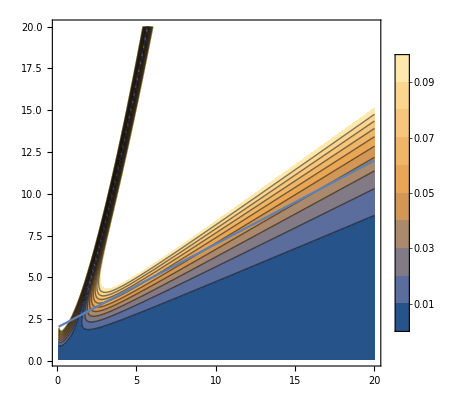

```mathematica
Show[
ListContourPlot[data,PlotLegends->Automatic,PlotRange->{0,0.1}],
Plot[2+0.5q,{q,0.1,20}]
]
```

#### q -> 0

```mathematica
(* h = 1/w + x, s=q H4 ~ x*)
H4[s_,w_]=Normal[FullSimplify[InverseSeries[Series[Sqrt[1+(1/w+x)^2]( w-1/(1/w + x)),{x,0,3}],s],w>0]]
```

(s^2 w)/((1+w^2)^2)+s/(w √(1+w^2))+(s^3 w (-3+2 w^2))/(2 (1+w^2)^(7/2))

```mathematica
HH4[q_,w_]=H4[q,w]+1/w
```

1/w+(q^2 w)/((1+w^2)^2)+q/(w √(1+w^2))+(q^3 w (-3+2 w^2))/(2 (1+w^2)^(7/2))

```mathematica
coef=Simplify[CoefficientList[Series[H4[q,w],{q,0,3}],q]]
```

{0,1/(w √(1+w^2)),w/((1+w^2)^2),(w (-3+2 w^2))/(2 (1+w^2)^(7/2))}

```mathematica
a=coef[[2]]
b=coef[[3]]
c=coef[[4]]
```

1/(w √(1+w^2))

w/((1+w^2)^2)

(-3 w+2 w^3)/(2 (1+w^2)^(7/2))

```mathematica
Simplify[c*a]
```

(-3+2 w^2)/(2 (1+w^2)^4)

```mathematica
Clear[a,b,c];
CForm[HornerForm[a*q+b*q^2+c q^3,q]]
```

q*(a + q*(b + c*q))

```mathematica
data4=Flatten[Table[{q,W,Abs[HH4[q,W]/SolP[q,W]-1]},{q,0.1,20,0.1},{W,0.1,20,0.1}],1];
```

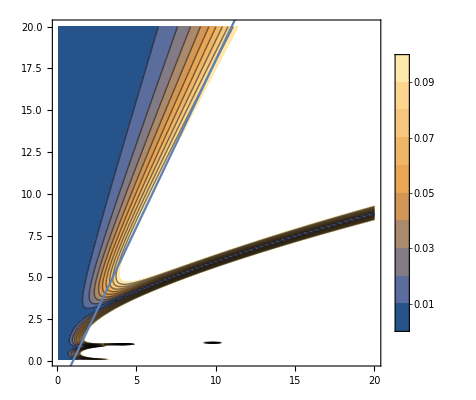

```mathematica
Show[
ListContourPlot[data4,PlotLegends->Automatic,PlotRange->{0,0.1}],
Plot[2(q-1),{q,0.1,20}]
]
```

## Testing

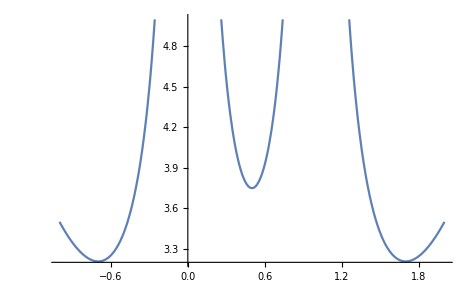

```mathematica
par={1,1,1};
Plot[Omega[x,0,0,par],{x,-1,2},PlotRange->{All,{Automatic,5}}]
```

```mathematica
FindMinimum[Omega[x,0,0,par],{x,-1}]
```

{3.2068,{x→-0.698406}}

```mathematica
FindMinimum[Omega[x,0,0,par],{x,0.5}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{3.75,{x→0.5}}

```mathematica
FindMinimum[Omega[x,0,0,par],{x,1.5}]
```

{3.2068,{x→1.69841}}

```mathematica
Omega0=10.;
s1=Sort[x/.Solve[Omega[x,0,0,par]==Omega0,x,Reals]]
CForm/@s1
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-2.59625,-0.111403,0.111438,0.888562,1.1114,3.59625}

{-2.5962495955220546,-0.1114029526954235,0.1114379246411004,0.8885620753588996,1.1114029526954234,3.5962495955220546}

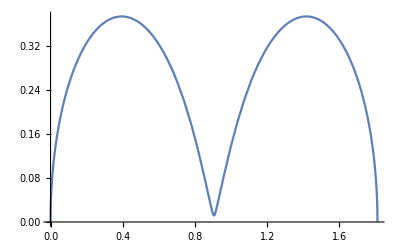

```mathematica
Block[{b,q,t,F,d,a,c,x0,x1,t0,T,Ft,FR,R,phi,s},
q=1;
d=1;
F=1;
a=d^3F^2;
b=a(1+q);
c=Cos[phi]^2;

phi=0; 
x0=s1[[2]];
x1=s1[[3]];

t0=x0/d;
T=(x1-x0)/d;

s=NDSolve[{R'[t]==-FCt[R[t],t+t0]/FCR[R[t],t+t0],R[0]==0},R,{t,0,T}];

Plot[Evaluate[Sqrt[R[t]/.s]],{t,0,T},PlotRange->All]
]
```

```mathematica
?CylRadius
```

Global`CylRadius

CylRadius[x_,phi_,Omega0_,{q_,F_,delta_}]:=Module[{t,R},t=x/delta;R/.NSolve[{FC[R,t]==delta Omega0,R>0},R]]

## Testing python wrapping for marching meshing

```mathematica
path="/home/horvat/Documents/work/phoebe/phoebe-code/sandbox/muki/";
```

```mathematica
Triangles=ReadList[path<>"py_meshingT.txt",Table[Number,{3}]];
Vertices=ReadList[path<>"py_meshingV.txt",Table[Real,{2},{3}]];
```

```mathematica
Graphics3D[
{
EdgeForm[],
Triangle[
Vertices[[#+1,1]]&/@Triangles
]
}
]
```

-Graphics3D-